```mathematica
legendre[n_,x_]:=LegendreP[n-1,2 x-1] √(2 (n-1)+1)
h[1,1,x_]:=If[Abs[x]>1,0,If[x≥0,1/(√2),-1/(√2)]]
h[2,1,x_]:=If[Abs[x]>1,0,If[x≥0,√(3/2) (-1+2 x),h[2,1,-x]]]
h[2,2,x_]:=If[Abs[x]>1,0,If[x≥0,√(1/2) (-2+3 x),-h[2,2,-x]]]
h[3,1,x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(1/2) (1-24 x+30 x^2),-h[3,1,-x]]]
h[3,2,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(3/2) (3-16 x+15 x^2),h[3,2,-x]]]
h[3,3,x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(5/2) (4-15 x+12 x^2),-h[3,3,-x]]]
h[4,1,x_]:=If[Abs[x]>1,0,If[x≥0, √(15/34) (1+4x-30 x^2+28 x^3),h[4,1,-x]]]
h[4,2,x_]:=If[Abs[x]>1,0,If[x≥0, √(1/42) (-4+105x-300 x^2+210 x^3),-h[4,2,-x]]]
h[4,3,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(35/34) (-5+48x-105 x^2+64 x^3),h[4,3,-x]]]
h[4,4,x_]:=If[Abs[x]>1,0,If[x≥0, 1/2 √(5/42) (-16+105x-192 x^2+105 x^3),-h[4,4,-x]]]
h[5,1,x_]:=If[Abs[x]>1,0,If[x≥0,√(1/186) (1+30x+210 x^2-840 x^3+630 x^4),-h[5,1,-x]]]
h[5,2,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(1/38) (-5-144x+1155 x^2-2240 x^3+1260 x^4),h[5,2,-x]]]
h[5,3,x_]:=If[Abs[x]>1,0,If[x≥0,√(35/14694) (22-735x+3504 x^2-5460 x^3+2700 x^4),-h[5,3,-x]]]
h[5,4,x_]:=If[Abs[x]>1,0,If[x≥0,1/8 √(21/38) (35-512x+1890 x^2-2560 x^3+1155 x^4),h[5,4,-x]]]
h[5,5,x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(7/158) (32-315x+960 x^2-1155 x^3+480 x^4),-h[5,5,-x]]]
```

```mathematica
fk[k_,fnumber_]:=h[k,fnumber,#]&
```

```mathematica
vk[k_,fnumber_,level_,place_]:=If[level==0,legendre[fnumber,#1]&,2^(level/2) fk[k,fnumber][2^level #1-(2 place-1)]&]
```

```mathematica
innerProduct[f_,g_,level_,place_]:=NIntegrate[f[x] g[x],{x,(place-1) 2^(-switch[level-1]),place 2^(-switch[level-1])}]

iteratek[k_,n_]:=Module[{fnumber,level,place,hashMap,count},
hashMap=Table[0,{i,1,k 2^n}];count=1;
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
hashMap⟦count++⟧={fnumber,level+1,place};
]]];

Return[hashMap];]
(*working*)


getCoefficientsk[k_,f_,fnumber_,level_,place_]:=innerProduct[f,vk[k,fnumber,level,place],level,place]

fullCoefficientsk[k_,f_,n_]:=Module[{iters,i,hash,count,coeff},
iters=iteratek[k,n];
hash=Table[0,{i,1,Length[iters]}];
For[i=1,i≤Length[iters],i++,
coeff=getCoefficientsk[k,f,iters⟦i⟧⟦1⟧,iters⟦i⟧⟦2⟧-1,iters⟦i⟧⟦3⟧];hash⟦i⟧=iters⟦i⟧->coeff;];Return[SparseArray[hash]]]

reconstructk[k_,coeffs_,x_,n_]:=Module[{fnumber,level,place,value},
value=0;
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤k,fnumber++,
value+=coeffs⟦fnumber,level+1,place⟧ vk[k,fnumber,level,place][x];
]]];Return[value]]
```

```mathematica
iteratek[4]
```

iteratek[4]

```mathematica
coeffsk=fullCoefficientsk[4,Sin[Pi #]&,4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained 1.21973×10^-17 and 1.38379×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.615219}. NIntegrate obtained -6.72205×10^-17 and 9.79356×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -3.33392×10^-17 and 1.66234×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

SparseArray[<64>, {4, 5, 8}]

```mathematica
dg2Error=Table[Sqrt[.0062 Sum[(reconstructk[2,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[2,Sin[Pi #]&,n]],{n,1,7}]//Quiet
```

{0.0632198,0.015956,0.00401919,0.00100416,0.000247567,0.0000635702,0.0000158689}

```mathematica
dg3Error=Table[Sqrt[.0062 Sum[(reconstructk[3,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[3,Sin[Pi #]&,n]],{n,1,6}]//Quiet
```

{0.00853766,0.00112029,0.00014118,0.0000179772,2.38176×10^-6,2.64473×10^-7}

```mathematica
dg1Error=Table[Sqrt[.0062 Sum[(reconstructk[1,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[1,Sin[Pi #]&,n]],{n,1,5}]//Quiet
dg2Error=Table[Sqrt[.0062 Sum[(reconstructk[2,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[2,Sin[Pi #]&,n]],{n,1,7}]//Quiet
dg3Error=Table[Sqrt[.0062 Sum[(reconstructk[3,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[3,Sin[Pi #]&,n]],{n,1,5}]//Quiet
dg4Error=Table[Sqrt[.0062 Sum[(reconstructk[4,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[4,Sin[Pi #]&,n]],{n,1,5}]//Quiet
```

{0.310658,0.161549,0.0813504,0.0407878,0.0205338}

{0.0632198,0.015956,0.00401919,0.00100416,0.000247567}

{0.00853766,0.00112029,0.00014118,0.0000179772,2.38176×10^-6}

{0.000846151,0.0000520552,3.26065×10^-6,2.00796×10^-7,1.21776×10^-8}

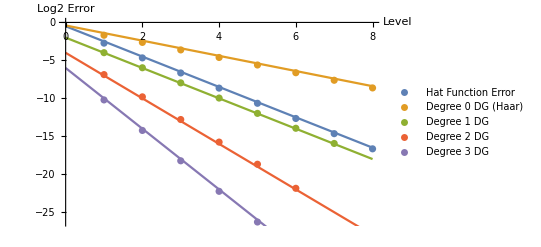

```mathematica
Show[ListPlot[{hatError,dg1Error,dg2Error,dg3Error,dg4Error}//Log2,PlotLegends->{"Hat Function Error", "Degree 0 DG (Haar)","Degree 1 DG","Degree 2 DG","Degree 3 DG"},AxesLabel->{"Level","Log2 Error"}],Plot[{-2x-.5,-x-.4,-2x-2,-3x-4,-4x-6},{x,0,8}]]
```